```mathematica
Exit
```

## Main Code

### Notes

#### Notes

From /ifs/jwst/wit/miri/pipelinetests/shared/README_build7.txt: 
jw11162001001_01101_00001_MIRIMAGE_uncal.fits
MIRM107-E-6021041029_1_493_SE_2016-01-21T04h22m18.fits -point source in imager
 (IMG_RAD_17) location at (702,452) slope ~ 300 on point source, 20 frames, 5
 ints.

### Functions

```mathematica
$HistoryLength=1;
```

```mathematica
mapFun[{x_,y_}]:={x+Floor[x/4],y}
submat[mat_,p1_,p2_]:=mat[[p1[[2]];;p2[[2]],p1[[1]];;p2[[1]]]]
```

```mathematica
ButtonFunPre[varr_,options_]:=Module[{var=ToExpression@varr},
Column@{Row@Flatten@Outer[Button[#,#2=#]&,#2,{#}],Style[Dynamic@#,Bold,16]}&[var,options]]
ButtonFun[var_,options_]:=Last[{Clear@#,ButtonFunPre[#,options]}&[var]]
```

```mathematica
ClearAll@TAFITSGenerate
TAFITSGenerate[imdataUsed_,partitionedPoses_,offset_,firstPix_,metastuff_,pointPose_,smallcutSize_,xdims_,ydims_,killCornersBool_]:=Module[{sciDims,length,pointPosesRel,pointPoses,refColLength,p01,p02,point2,pp1,pp2,dims,numba,image,sciImage,refInfo,newRef,smallcut,p1,p2,blankIm3,resPre,numRowsColsToZero=5,cubeNoRefColumns,allRefData,onesMask,cubeMask,resultingDataCube,res,finIm,result},
sciDims=Drop[Dimensions@imdataUsed,1];
length=First@sciDims;
pointPosesRel=partitionedPoses-offset;
pointPoses=pointPosesRel+ConstantArray[firstPix,Length@pointPosesRel];
refColLength=First["NREFIMG"/.metastuff[[1]]];

p01=pointPose-smallcutSize;
p02=pointPose+smallcutSize;
point2=(firstPix+{xdims,ydims})-1;
pp1=mapFun[firstPix];
pp2=mapFun[point2];

dims={refColLength,Last@sciDims};
numba=length-refColLength;
cubeNoRefColumns=imdataUsed[[All,1;;length-refColLength]];
ClearSystemCache[];
resultingDataCube=If[killCornersBool,
onesMask=ConstantArray[1.0,Drop[Dimensions@cubeNoRefColumns,1]];
onesMask[[-numRowsColsToZero;;-1]]=ConstantArray[0.0,Dimensions@onesMask[[-numRowsColsToZero;;-1]]];
onesMask[[1;;numRowsColsToZero]]=ConstantArray[0.0,Dimensions@onesMask[[1;;numRowsColsToZero]]];
onesMask[[;;,-numRowsColsToZero;;-1]]=ConstantArray[0.0,Dimensions@onesMask[[;;,-numRowsColsToZero;;-1]]];
onesMask[[;;,1;;numRowsColsToZero]]=ConstantArray[0.0,Dimensions@onesMask[[;;,1;;numRowsColsToZero]]];
cubeMask=ConstantArray[onesMask,Length@cubeNoRefColumns];
cubeMask*cubeNoRefColumns,
cubeNoRefColumns
];
allRefData=imdataUsed[[All,length-(refColLength-1);;length]];

Table[
Print[num];
ClearSystemCache[];
sciImage=resultingDataCube[[num]];
refInfo=allRefData[[num]];
newRef=Partition[Flatten[refInfo],numba];
smallcut=submat[sciImage,p01,p02];
Table[
{p1,p2}={#-smallcutSize,#+smallcutSize}&[pointPoses[[k]]];
sciImage[[p1[[2]];;p2[[2]],p1[[1]];;p2[[1]]]]=smallcut,{k,Length@pointPoses}];
blankIm3=Transpose@Partition[Flatten@Riffle[Flatten[Transpose@sciImage],newRef,{4*(numba)+1,-1,4*(numba)+1}],numba];
result=submat[blankIm3,pp1,pp2];
{result,Max@result}
,{num,Length@imdataUsed}]
]
```

```mathematica
AssThread[var_]:=Association@Thread[var]
```

```mathematica
ClearAll@OSSTADatGenFun
OSSTADatGenFun[TASub_,associationData_,frameTimeAss_,siafEntriesPre3_,imdata0_,offset_,metastuff_,pointPose_,smallcutSize_,maxNum_,killCornersBool_,numFrames_]:=Module[{keysofInterest,associationSub,aperName,rois,mode,subarray,frametime,subarrayQ,siafEntry,
xdims,ydims,roiSizes,roiLocations,firstPix,lensROIS,diff,pointSourceLocationsOnFullArray,partitionedPosesPre,partitionedPoses,g1,point2,check,finIm,alldaframes,numImagesToMake,difs,ldif,totnum,intlist,finIntList,imdataUsed,allresesPre,allreses,datPre,exportFilenameBase,filename,preFileDir,outDir,pydir,themeat,pointString,ngroupOFile,inputFileReadout,text,redMeDir,maxAllReses,allresesFIN,allresesPrePre,tf,allresesAndMaxes,allMaxes,normNum,roiSiafEntries,xDetRef,yDetRef,xSciRef,ySciRef,keysLocation
},
associationSub=associationData[TASub];
rois=associationSub["ROIs"];
aperName=associationSub["AperName"];

siafEntry=aperName/.siafEntriesPre3;
keysofInterest={"XSciSize","YSciSize"};
keysLocation={"XDetRef","YDetRef","XSciRef","YSciRef"};
{xdims,ydims}=Map[ToExpression,keysofInterest/.siafEntry];
roiSiafEntries=rois/.siafEntriesPre3;
roiSizes=Map[ToExpression,keysofInterest/.roiSiafEntries,{2}];
roiLocations=Table[
{xDetRef,yDetRef,xSciRef,ySciRef}=ToExpression/@(keysLocation/.roiSiafEntries[[k]]);
Round[{xDetRef-xSciRef+1,yDetRef-ySciRef+1}],{k,Length@roiSiafEntries}];
{xDetRef,yDetRef,xSciRef,ySciRef}=ToExpression/@(keysLocation/.siafEntry);
firstPix=Round[{xDetRef-xSciRef+1,yDetRef-ySciRef+1}];

lensROIS=First/@(roiSizes/2);
diff=Which[Evaluate[whichSequence[TASub,lensROIS]]];
pointSourceLocationsOnFullArray=roiLocations+roiSizes/2+1;
partitionedPosesPre=pointSourceLocationsOnFullArray-ConstantArray[firstPix,Length@roiLocations];
partitionedPoses=partitionedPosesPre+diff;

alldaframes=Reverse[(Length@imdata0+1)-Range@numFrames];

Print["start making cube"];
If[MemberQ[alldaframes,_?(#≤0&)],
numImagesToMake=numFrames-Length@imdata0;
difs=Differences[imdata0][[Round[Length@imdata0*0.25];;Round[Length@imdata0*0.75]]];
ldif=Length@difs;
totnum=Ceiling[numImagesToMake/ldif];
intlist=Table[RandomSample[Range[ldif],ldif],totnum];
finIntList=Flatten[intlist][[1;;numImagesToMake]];
ClearSystemCache[];
imdataUsed=Join[imdata0,Drop[Accumulate@Prepend[difs[[finIntList]],Last@imdata0],1]];
,
imdataUsed=imdata0[[alldaframes]];
];
Print["end making cube"];
allresesAndMaxes=TAFITSGenerate[imdataUsed,partitionedPoses,offset,firstPix,metastuff,pointPose,smallcutSize,xdims,ydims,killCornersBool];
Print["Finished"];
allreses=allresesAndMaxes[[All,1]];
allMaxes=allresesAndMaxes[[All,2]];
maxAllReses=N@Max@allMaxes;
tf=maxAllReses>maxNum;
If[tf,normNum=maxNum/maxAllReses;allreses*=normNum;];
Print["Finished Normalizing"];
{firstPix,xdims,ydims,allreses,partitionedPoses,associationSub,roiSizes,roiLocations}
]
```

```mathematica
ClearAll@ExportFun
```

```mathematica
ExportFun[TASub_,associationSub_,readoutMode_,numFrames_,numFramesAfterAVG_,prefileLocation_,nbdir_,allreses_,cv3Dir_,pythonLocation_,partitionedPoses_,metastuff_,siafLocation_,inputImage_,repoDir_,roiSizes_,pointPose_,numImsInGroup_,killCornersBool_,firstPix_,xdims_,ydims_,roiLocations_,p2_,frameTimeAss_,newNamingAssociation_,sourceLocationsInROI_]:=Module[{exportFilenameBase,filename,preFileDir,outDir,themeat,text,redMeDir,pydir,mode,subarray,frametime,subarrayQ,g1,finIm,config,subarrayName},

subarray=associationSub["Subarray"];
frametime=frameTimeAss[subarray];
subarrayQ=If[subarray=="FULL",False,True];

{config,subarrayName}=newNamingAssociation[TASub];
exportFilenameBase=config<>"_"<>readoutMode<>"_"<>subarrayName<>"_"<>ToString@numFramesAfterAVG;

filename=exportFilenameBase<>"_pre.fits";
preFileDir=FileNameJoin[{prefileLocation,filename}];
outDir=FileNameJoin[{nbdir,"OSS_Delivery","delivery_files",exportFilenameBase<>".fits"}];

Export[preFileDir,allreses];
If[FileExistsQ@outDir,DeleteFile[outDir]];pydir=FileNameJoin[{nbdir,"OSS_TA_Package2.py"}];
themeat="\""<>pydir<>"\" \""<>cv3Dir<>"\" \""<>preFileDir<>"\" \""<>outDir<>"\" "<>ToString@frametime<>" "<>ToString@subarrayQ;
Run[StringDrop[pythonLocation,1]<>" "<>themeat];

text=ReadMeText[partitionedPoses,metastuff,outDir,siafLocation,inputImage,repoDir,readoutMode,numFrames,numFramesAfterAVG,roiSizes,pointPose,numImsInGroup,killCornersBool,sourceLocationsInROI];
redMeDir=FileNameJoin[{nbdir,"OSS_Delivery","delivery_files",exportFilenameBase<>"_README.txt"}];Export[redMeDir,text];

g1=Graphics[{Opacity[0.5],LightBlue,Rectangle[firstPix,firstPix+{xdims,ydims}],LightRed,Sequence@@(Rectangle[#[[1]],#[[2]]]&/@Transpose@{roiLocations,roiLocations+roiSizes}),Black,Opacity[1.0],Sequence@@(Disk[#,1]&/@(partitionedPoses+ConstantArray[firstPix,Length@roiLocations]))}];
finIm=Show[p2,g1,ImageSize->1000];
Export[FileNameJoin[{nbdir,"OSS_Delivery","delivery_files",exportFilenameBase<>"_pointsource_location.png"}],finIm];
Print[outDir];
]
```

```mathematica
ReadMeText[partitionedPoses_,metastuff_,outDir_,siafLocation_,inputImage_,repoDir_,readoutMode_,numFrames_,numFramesAfterAVG_,roiSizes_,pointPose_,numImsInGroup_,killCornersBool_,sourceLocationsInROI_]:=Module[{pointString,ngroupOFile,inputFileReadout,pointStringDet,pointStringROI,finStringTMP},
pointString="\n\t"<>StringRiffle[("{X,Y}= "<>ToString[mapFun[#]])&/@partitionedPoses,"\n\t"];
pointStringDet="\n\t"<>StringRiffle[("{X,Y}= "<>ToString[#])&/@partitionedPoses,"\n\t"];
pointStringROI="\n\t"<>StringRiffle[ToString/@sourceLocationsInROI,"\n\t"];

finStringTMP="\tMIRIM_TA1065_UL -> {25, 25}\tMIRIM_TA1140_UL -> {24, 28}\tMIRIM_TA1550_UL -> {24, 25}\n\tMIRIM_TA1065_UR -> {25, 25}\tMIRIM_TA1140_UR -> {27, 28}\tMIRIM_TA1550_UR -> {27, 33}\n\tMIRIM_TA1065_LL -> {25, 25}\tMIRIM_TA1140_LL -> {25, 29}\tMIRIM_TA1550_LL -> {22, 25}\n\tMIRIM_TA1065_LR -> {25, 25}\tMIRIM_TA1140_LR -> {25, 28}\tMIRIM_TA1550_LR -> {25, 27}\n\tMIRIM_TA1065_CUL -> {9, 7}\tMIRIM_TA1140_CUL -> {9, 11}\tMIRIM_TA1550_CUL -> {7, 11}\n\tMIRIM_TA1065_CUR -> {9, 5}\tMIRIM_TA1140_CUR -> {7, 7}\tMIRIM_TA1550_CUR -> {11, 10}\n\tMIRIM_TA1065_CLL -> {9, 8}\tMIRIM_TA1140_CLL -> {9, 11}\tMIRIM_TA1550_CLL -> {6, 9}\n\tMIRIM_TA1065_CLR -> {9, 8}\tMIRIM_TA1140_CLR -> {9, 11}\tMIRIM_TA1550_CLR -> {9, 10}";
If[TASub=="MASK1065",pointStringROI="\n"<>finStringTMP];

ngroupOFile=("NINT"/.metastuff)[[1,1]];
inputFileReadout=("READOUT"/.metastuff)[[1,1]];
"README for "<>FileNameTake@outDir<>", hereafter referred to as Delivered_FITS_File.
- Size and location of ROIs are taken from the the MIRI SIAF excel file: "<>FileNameTake@siafLocation<>"
- All {X,Y} locations are given using the SIAF pixel location scheme - note this coordinate system is the same as the one used in DS9.
- Delivered_FITS_File generated from CV3 FITS file "<>inputImage<>", hereafter referred to as Origin_FITS_File,  located in "<>repoDir<>"
- Delivered_FITS_File is for use in testing READOUT = "<>readoutMode<>"
- Origin_FITS_File has "<>inputFileReadout<>" readout pattern
- Delivered_FITS_File has NGROUP = "<>ToString@numFrames<>"
- After averaging, Delivered_FITS_File would have NGROUP = "<>ToString@numFramesAfterAVG<>" for READOUT = "<>readoutMode<>"
- For each image in Delivered_FITS_File, every 5th column of the image contains reference pixels
- "<>ToString@Length@roiSizes<>" ROI locations for this subarray, with 1 point source located in each ROI.
- Each point source in Delivered_FITS_File is a copy and pasted 3x3 cut out of a CV3 point source in Origin_FITS_File, whose center pixel is located at {X,Y} = "<>ToString@pointPose<>" in Origin_FITS_File. 
- For each image in Delivered_FITS_File, the center pixel for the injected point source(s) are located at:"<>pointString<>"\n- Without the reference columns, the point sources' center pixels are located at the following locations on the FULL array (these numbers are obtained by multiplying the x-values in the numbers above by 0.8):"<>pointStringDet<>"
- Within the ROI, the point sources' center pixels are located at the following locations:"<>pointStringROI<>"
- Origin_FITS_File contains "<>ToString@ngroupOFile<>" integrations with "<>ToString@numImsInGroup<>" groups each. 
- Delivered_FITS_File made with the last NGROUP groups of the last integration of the Origin_FITS_File. If NGROUP > the number of frames contained in the last integration of Origin_FITS_File, then extra data was made (taken from Origin_FITS_File) to extend the integration.  
- Only the following FITS keywords are accounted for in the Delivered_FITS_File: 'FILENAME', ‘READOUT’, 'NGROUP', 'TFRAME', 'NINT', 'SUBARRAY', 'NAXIS', 'NAXIS1', 'NAXIS2', 'NAXIS3', 'INTTIME', 'EXPTIME', 'NCOLS', 'NROWS', 'BSCALE', 'BZERO', 'BITPIX’. All other keywords were directly inherited from Origin_FITS_File and have not been verified to be correct.

"<>If[killCornersBool,"- First and last 5 rows and first and last 5 columns of the FULL frame science image have been set to value 0.0 - some of the ROIs are close to the edge of the FULL array and the edges contain noisy pixels which can interfere with the centroid.
",""]<>"
Delivery made by J. Brendan Hagan for OSS target acquisition testing.
Delivery Date: "<>StringTrim@StringDrop[DateString[],-8]
]
```

```mathematica
ClearAll@whichSequence
```

```mathematica
whichSequence[TASub_,lensROIS_]:=Sequence@@{TASub=="MASKLYOT",lyotManual,TASub=="MASK1065",qPM4manual,TASub=="MASK1140",qPM4manual,TASub=="MASK1550",qPM4manual,TASub=="LRS_FULL",LRSfullManual,TASub=="MRS",MRSManual,TASub=="LRS_SUBPRISM",LRSSlitManual,True,(RandomInteger[{-(#/2-1),#/2-1},2]&/@lensROIS)};
```

```mathematica
ClearAll@DatGenOSS
```

```mathematica
DatGenOSS[{TASub_,numFrames_,readoutMode_}]:=OSSTADatGenFun[TASub,numFrames,readoutMode,associationData,frameTimeAss,siafEntriesPre3,pythonLocation,cornerScriptLocation,siafLocation,print,p2,ilumIm,imdata0,offset,metastuff,pointPose,smallcutSize,prefileLocation,nbdir,cv3Dir,inputImage,repoDir,numImsInGroup,maxNum,killCornersBool]
```

### script init

https://github.com/spacetelescope/pysiaf/tree/master/pysiaf/prd_data/JWST/PRDOPSSOC-H-015/SIAFXML

```mathematica
local=True;
nbdir=NotebookDirectory[];
fnSplit=FileNameSplit[nbdir];
miriDirectory=DirectoryName[nbdir,Length@fnSplit-Position[fnSplit,"MIRI"][[1,1]]];
prefileLocation=FileNameJoin[{nbdir,"OSS_Delivery","pre_files"}];
repoDir="/ifs/jwst/wit/miri/pipelinetests/testdata/";
dir=If[local,FileNameJoin[{nbdir,"MIRIM2","golden_file"}],repoDir];
inputImage="MIRM107-E-6021041029_1_493_SE_2016-01-21T04h22m18.fits";
```

```mathematica
cv3Dir=FileNameJoin[{nbdir,inputImage}];
metastuff=Import[cv3Dir,"Metadata"];
bzero=("BZERO"/.metastuff)[[1,1]];
Print[bzero,"   ",("BSCALE"/.metastuff)[[1,1]]];
```

32768   1

```mathematica
Needs["Developer`"]
```

```mathematica
indat=Import[cv3Dir,"RawData"];
imdata00=indat[[1]];imdata00=imdata00+bzero;
Print[Dimensions@imdata00];
numImsInGroup=("NGROUP"/.metastuff)[[1,1]];
imdata0=ToPackedArray[N@imdata00[[-numImsInGroup;;-1]]];
```

{100,1280,1032}

```mathematica
imdata0//Dimensions
```

{20,1280,1032}

```mathematica
ArrayPlot[imdata0[[1]],DataReversed->True]
```

-Graphics-

```mathematica
ilumIm=First@Import[First@FileNames["f1065c.fits",nbdir],"RawData"];
pic2=ArrayPlot[ilumIm,DataReversed->True];
```

```mathematica
pointPose={701,451};
smallcutSize=1;
offset=1;(*Mathematica indexing starts at 1, indexing for subarray locations starts at 0*)
```

```mathematica
pythonLocation="!/Users/hagan/anaconda3/bin/python";
siafLocation=FileNameJoin[{nbdir,"MIRI_SIAF.xml"}];(*miriDirectory<>"MIRI_Documents/MIRI_SIAF/MIRI_SIAF.xml";*)
```

```mathematica
miriSiafXML=Import[siafLocation];
siafEntriesPre=Cases[miriSiafXML,XMLElement["SiafEntry",_,x_]->x,Infinity];
siafEntriesPre2=Flatten[Cases[#,XMLElement[x_,_,{y_}]->{x->y},{1}]]&/@siafEntriesPre;
instrums="InstrName"/.siafEntriesPre2;
apNames="AperName"/.siafEntriesPre2;
siafEntriesPre3=Table[apNames[[k]]-> Complement[siafEntriesPre2[[k]],{"InstrName"->instrums[[k]],"AperName"->apNames[[k]]}],{k,Length@siafEntriesPre2}];

mykeywords={"AperName","ROIs","Mode","Subarray"};
lyotROIs={"MIRIM_TALYOT_UL","MIRIM_TALYOT_UR","MIRIM_TALYOT_LL","MIRIM_TALYOT_LR","MIRIM_TALYOT_CUL","MIRIM_TALYOT_CUR","MIRIM_TALYOT_CLL","MIRIM_TALYOT_CLR"};
filters4qPMs={"1065","1140","1550"};
roiNames4QPMs=Association@Table[filter->{"MIRIM_TA"<>filter<>"_UL","MIRIM_TA"<>filter<>"_UR","MIRIM_TA"<>filter<>"_LL","MIRIM_TA"<>filter<>"_LR","MIRIM_TA"<>filter<>"_CUL","MIRIM_TA"<>filter<>"_CUR","MIRIM_TA"<>filter<>"_CLL","MIRIM_TA"<>filter<>"_CLR"},{filter,filters4qPMs}];
lrsFullROIs={"MIRIM_TALRS"};
lrsSubPrismROIs={"MIRIM_TASLITLESSPRISM"(*,"MIRIM_SLITLESSUPPER","MIRIM_SLITLESSLOWER"*)};
mrsROIs={"MIRIM_TAMRS"};
```

```mathematica
associationData=Association@{
"MASKLYOT"->AssThread[mykeywords->{"MIRIM_MASKLYOT",lyotROIs,"CORON","LYOT"}],
"MASK"<>#->AssThread[mykeywords->{"MIRIM_MASK"<>#,roiNames4QPMs[#],"CORON","4QPM"}]&["1065"],
"MASK"<>#->AssThread[mykeywords->{"MIRIM_MASK"<>#,roiNames4QPMs[#],"CORON","4QPM"}]&["1140"],
"MASK"<>#->AssThread[mykeywords->{"MIRIM_MASK"<>#,roiNames4QPMs[#],"CORON","4QPM"}]&["1550"],
"LRS_SUBPRISM"->AssThread[mykeywords->{"MIRIM_SLITLESSPRISM",lrsSubPrismROIs,"LRS","SUBPRISM"}],
"LRS_FULL"->AssThread[mykeywords->{"MIRIM_FULL",lrsFullROIs,"LRS","FULL"}],
"MRS"->AssThread[mykeywords->{"MIRIM_FULL",mrsROIs,"MRS","FULL"}]};
```

FAST readout times taken from tables 1, 2, and 3 in https://jwst-docs.stsci.edu/display/JTI/MIRI+Detector+Subarrays #MIRIDetectorSubarrays-SubarrayReadout

```mathematica
frameTimeAss=Association@{
"LYOT"->0.324,
"4QPM"->0.24,
"FULL"->2.775,
"SUBPRISM"->0.159
};
```

```mathematica
Keys@associationData
```

{MASKLYOT,MASK1065,MASK1140,MASK1550,LRS_SUBPRISM,LRS_FULL,MRS}

```mathematica
(*Offsets for point source placement in each ROI relative to the cenmter of the ROI*)
lyotManual=ConstantArray[{0,0},Length@associationData["MASKLYOT"]["ROIs"]];
qPM4manual={{0,0},{0,0},{0,0},{0,0},{0,-2},{0,-4},{0,-1},{0,-1}};
LRSfullManual={{0,0}};
MRSManual={{0,0}};
LRSSlitManual={{0,0}};
```

```mathematica
maxNum=2^16-1.0
(*maximum number that can be accurately represented in BITPIX = 16 FITS file*)
```

65535.

```mathematica
(*print images of *)
print=False;
killCornersBool=False;
```

```mathematica
newNamingAssociation=Association@{
"MASKLYOT"->{"MIRLYOT","MASKLYOT"},
"MASK1065"->{"MIR4QPM","MASKnnnn"},
(*"MASK1140"->{"MIR4QPM","MASKnnnn"},
"MASK1065"->{"MIR4QPM","MASKnnnn"},*)
"LRS_SUBPRISM"->{"MIRLRS","SUBPRISM"},
"LRS_FULL"->{"MIRLRS","FULL"},
"MRS"->{"MIRMRSALL","FULL"}}
```

<|MASKLYOT→{MIRLYOT,MASKLYOT},MASK1065→{MIR4QPM,MASKnnnn},LRS_SUBPRISM→{MIRLRS,SUBPRISM},LRS_FULL→{MIRLRS,FULL},MRS→{MIRMRSALL,FULL}|>

```mathematica
readoutAssociation=Association[Rule@@@Transpose@{{"FAST","FASTGRPAVG","FASTGRPAVG8","FASTGRPAVG16","FASTGRPAVG32","FASTGRPAVG64"},{1,4,8,16,32,64}}];
```

## this it

```mathematica
ParamGen:={#1,#2,Which[#1=="FAST",#3,#1=="FASTGRPAVG",#3*4,True,#3*ToExpression@StringDelete[#1,"FASTGRPAVG"]],#3}&
```

```mathematica
finTablePre={{"FASTGRPAVG16","MASK1065",4}(*,{"FASTGRPAVG16","MASK1065",98},{"FASTGRPAVG32","MASK1065",4},{"FASTGRPAVG32","MASK1065",66},{"FASTGRPAVG32","MASK1065",98},{"FASTGRPAVG64","MASK1065",4},{"FASTGRPAVG64","MASK1065",98},{"FASTGRPAVG8","MASK1065",4},{"FASTGRPAVG8","MASK1065",98},{"FASTGRPAVG","MASK1065",36},{"FASTGRPAVG","MASK1065",4},{"FASTGRPAVG","MASK1065",66},{"FASTGRPAVG","MASK1065",98},{"FAST","MASK1065",4},{"FAST","MASK1065",98}*)};
finTable0=ParamGen[Sequence@@#]&/@finTablePre;
finTable=finTable0[[Ordering@finTable0[[All,3]]]]
```

{{FASTGRPAVG16,MASK1065,64,4}}

```mathematica
Table[
{readoutMode,TASub,numFrames,numFramesAfterAVG}=finTable[[k]];
alldaframes=Reverse[(Length@imdata0+1)-Range@numFrames];
sciDims=Drop[Dimensions@imdata0,1];
length=First@sciDims;
refColLength=First["NREFIMG"/.metastuff[[1]]];
imdata00=If[ numFrames<Length@imdata0,imdata0[[alldaframes]],imdata0];
allRefData=imdata00[[All,length-(refColLength-1);;length]];
cubeNoRefColumns=imdata00[[All,1;;length-refColLength]];
associationSub=associationData[TASub];
rois=associationSub["ROIs"];
aperName=associationSub["AperName"];

siafEntry=aperName/.siafEntriesPre3;
keysofInterest={"XSciSize","YSciSize"};
keysLocation={"XDetRef","YDetRef","XSciRef","YSciRef"};
{xdims,ydims}=Map[ToExpression,keysofInterest/.siafEntry];
roiSiafEntries=rois/.siafEntriesPre3;
roiSizes=Map[ToExpression,keysofInterest/.roiSiafEntries,{2}];
roiLocations=Table[
{xDetRef,yDetRef,xSciRef,ySciRef}=ToExpression/@(keysLocation/.roiSiafEntries[[k]]);
Round[{xDetRef-xSciRef+1,yDetRef-ySciRef+1}],{k,Length@roiSiafEntries}];
{xDetRef,yDetRef,xSciRef,ySciRef}=ToExpression/@(keysLocation/.siafEntry);
firstPix=Round[{xDetRef-xSciRef+1,yDetRef-ySciRef+1}];
roiLocationsInSubarray=(#-(firstPix-1)&/@roiLocations);
lensROIS=First/@(roiSizes/2);
diff=Which[Evaluate[whichSequence[TASub,lensROIS]]];
pointSourceLocationsOnFullArray=roiLocations+roiSizes/2+1;
partitionedPosesPre=pointSourceLocationsOnFullArray-ConstantArray[firstPix,Length@roiLocations];
partitionedPoses=partitionedPosesPre+diff;
sourceLocationsInROIPre=Transpose@{rois,First/@Table[(#-(roiLocationsInSubarray[[kk]]-1)&/@{partitionedPoses[[kk]]}),{kk,Length@partitionedPoses}]};
sourceLocationsInROI=Thread[sourceLocationsInROIPre[[All,1]]->sourceLocationsInROIPre[[All,2]]];
pointPosesRel=partitionedPoses-offset;
pointPoses=pointPosesRel+ConstantArray[firstPix,Length@pointPosesRel];
p01=pointPose-smallcutSize;
p02=pointPose+smallcutSize;
point2=(firstPix+{xdims,ydims})-1;
pp1=mapFun[firstPix];
pp2=mapFun[point2];
numba=length-refColLength;

imdata1=Table[
sciImage=cubeNoRefColumns[[num]];
refInfo=allRefData[[num]];
newRef=Partition[Flatten[refInfo],numba];
smallcut=submat[sciImage,p01,p02];
Table[
{p1,p2}={#-smallcutSize,#+smallcutSize}&[pointPoses[[k]]];
sciImage[[p1[[2]];;p2[[2]],p1[[1]];;p2[[1]]]]=smallcut,{k,Length@pointPoses}];
blankIm3=Transpose@Partition[Flatten@Riffle[Flatten[Transpose@sciImage],newRef,{4*(numba)+1,-1,4*(numba)+1}],numba];
result=submat[blankIm3,pp1,pp2]
,{num,Length@cubeNoRefColumns}];
printIntList=False;

ClearSystemCache[];

If[MemberQ[alldaframes,_?(#≤0&)],
numImagesToMake=numFrames-Length@imdata1;
difs=Differences[imdata1][[Round[Length@imdata1*0.25];;Round[Length@imdata1*0.75]]];
ldif=Length@difs;
totnum=Ceiling[numImagesToMake/ldif];
intlist=Table[RandomSample[Range[ldif],ldif],totnum];
finIntList=Flatten[intlist][[1;;numImagesToMake]];
If[printIntList,Print["finIntList = ",finIntList];];
difImages=difs[[finIntList]];
accCube=Prepend[difImages,Last@imdata1];
imdataUsed=Join[imdata1,Drop[Accumulate[accCube],1]];
,
imdataUsed=imdata1;
];
maxVal=Max@imdataUsed;
tf=maxVal>maxNum;
If[tf,normNum=maxNum/maxVal;imdataUsed*=normNum;];

ExportFun[TASub,associationSub,readoutMode,numFrames,numFramesAfterAVG,prefileLocation,nbdir,imdataUsed,cv3Dir,pythonLocation,partitionedPoses,metastuff,siafLocation,inputImage,repoDir,roiSizes,pointPose,numImsInGroup,killCornersBool,firstPix,xdims,ydims,roiLocations,pic2,frameTimeAss,newNamingAssociation,sourceLocationsInROI],{k,Length@finTable}];
```

/Users/hagan/Master_Folder/James_Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/MIRI_TA/OSS_Delivery/delivery_files/MIR4QPM_FASTGRPAVG16_MASKnnnn_4.fits

## check

```mathematica
point2=(firstPix+{xdims,ydims})-1
```

{288,242}

```mathematica
checkO=True;
If[checkO,
check=submat[ilumIm,firstPix,point2];
ArrayPlot[check,DataReversed->True]]
```

-Graphics-

```mathematica
resPre=Last@datPre;
```

Last::normal: Nonatomic expression expected at position 1 in Last[datPre].

```mathematica
allreses//Dimensions
```

{5,304,400}

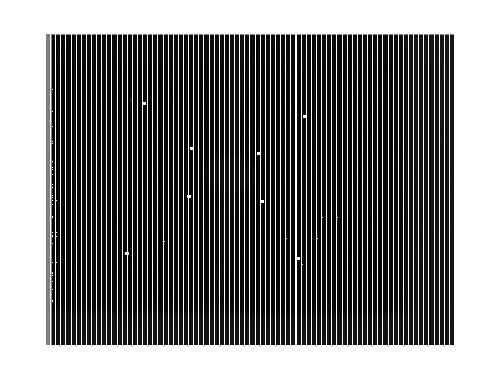

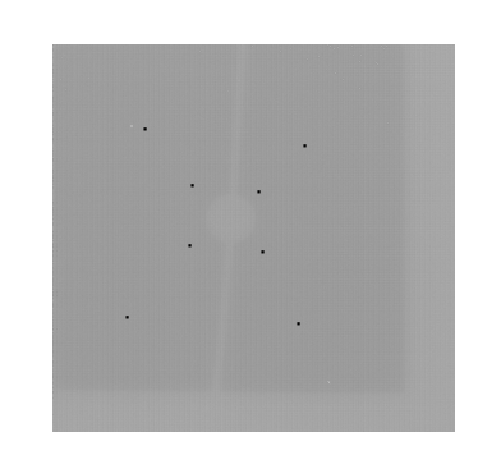

-Graphics-

-Graphics--Graphics-

```mathematica
men=Flatten@Last@allreses//Mean//N;
ArrayPlot[Last@allreses,DataReversed->True,ImageSize->500,PlotRange->{-men,men}*1.005]
check1=ArrayPlot[resPre,(*PlotRange->{-men,men}*1.005,*)DataReversed->True,ImageSize->500]
check2=ArrayPlot[check,(*PlotRange->{-men,men}*1.005,*)DataReversed->True,ImageSize->500]
Overlay[{check2,SetAlphaChannel[check1,.4]}]
```

```mathematica
mappedPoses=mapFun/@partitionedPoses;
Text@StringRiffle[("{X,Y} = "<>ToString@#)&/@mappedPoses,", "]
```

{X,Y} = {97, 237}, {X,Y} = {253, 224}, {X,Y} = {80, 90}, {X,Y} = {247, 85}, {X,Y} = {143, 193}, {X,Y} = {208, 188}, {X,Y} = {141, 146}, {X,Y} = {212, 141}

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

{Null,Null,Null,Null,Null,Null,Null,Null}

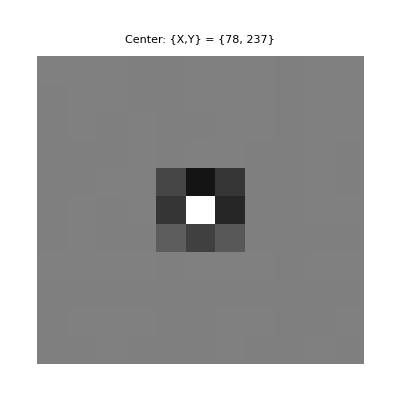

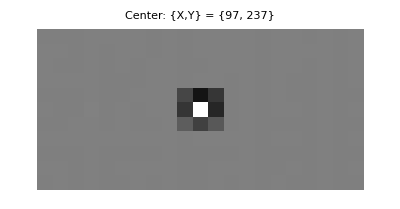

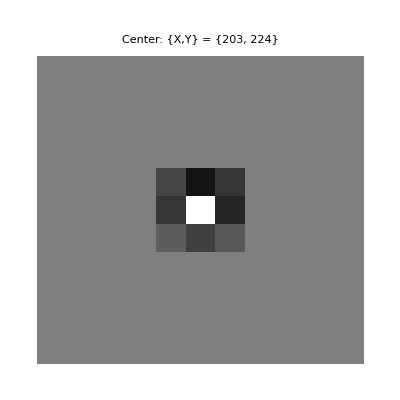

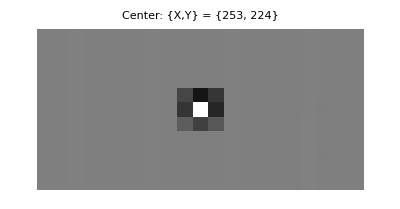

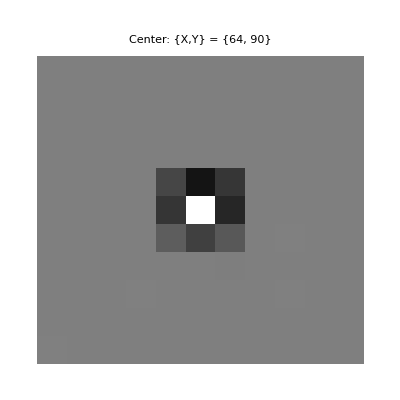

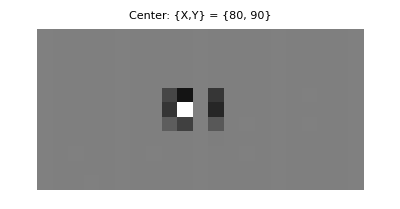

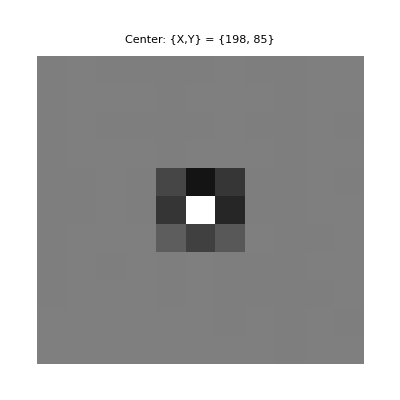

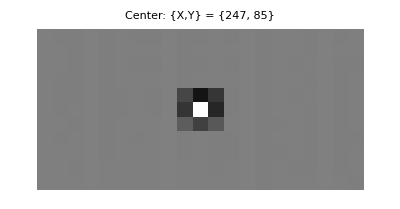

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
med=Median@Flatten@resPre;n=30000;
num=5;
Table[
{cn,rn}=partitionedPoses[[k]];
Print[ArrayPlot[resPre[[rn-num;;rn+num]][[;;,cn-num;;cn+num]],DataReversed->True,PlotRange->{med-n,med+n},PlotLabel->Style["Center: {X,Y} = "<>ToString@{cn,rn},18]]];
{cn2,rn2}=mapFun[{cn,rn}];
Print[ArrayPlot[Last[allreses][[rn2-num;;rn2+num]][[;;,cn2-2num;;cn2+2num]],DataReversed->True,PlotRange->{med-n,med+n},PlotLabel->Style["Center: {X,Y} = "<>ToString@{cn2,rn2},18]]];
,{k,Length@partitionedPoses}]
```

SetEnvironment[“HOME”→”/Users/adamg/”]

```mathematica
Environment["PATH"]
```

/usr/bin:/bin:/usr/sbin:/sbin

## Binary Files

### script

```mathematica
TASub
```

MASKLYOT

```mathematica
associationSub=associationData[TASub];
rois=associationSub["ROIs"];
aperName=associationSub["AperName"];
siafEntry=aperName/.siafEntriesPre3;
keysofInterest={"XSciSize","YSciSize"};
{xdims,ydims}=Map[ToExpression,keysofInterest/.siafEntry];
roiSizes=Map[ToExpression,keysofInterest/.(rois/.siafEntriesPre3),{2}];
roiLocations=ToExpression@(Import[StringRiffle[{pythonLocation,"\""<>cornerScriptLocation<>"\"","\""<>siafLocation<>"\"",#}],"String"]&/@rois);
roiEndLocations=(roiLocations)+roiSizes;
```

```mathematica
roiSizes
```

{{48,48},{48,48},{48,48},{48,48},{16,16},{16,16},{16,16},{16,16}}

```mathematica
roiLocationsOnSub=mapFun/@(roiLocations-ConstantArray[firstPix-1,Length@roiLocations])
roiEndLocationsOnSub=mapFun/@(roiEndLocations-ConstantArray[firstPix,Length@roiLocations])
```

{{58,212},{236,214},{52,74},{236,73},{138,184},{205,185},{136,138},{206,138}}

{{117,259},{295,261},{111,121},{295,120},{157,199},{223,200},{155,153},{225,153}}

```mathematica
allrois=Table[Round@Table[submat[allreses[[j]],roiLocationsOnSub[[k]],roiEndLocationsOnSub[[k]]],{k,Length@roiLocationsOnSub}],{j,Length@allreses}];
```

```mathematica
cubeBigROIs=allrois[[All,1]];
%//Dimensions
cubeSmallROIs=allrois[[All,5]];
%//Dimensions
```

{99,48,60}

{99,16,20}

```mathematica
48*60
```

2880

```mathematica
16*20
```

320

```mathematica
rois[[1]]
rois[[5]]
```

MIRIM_TALYOT_UL

MIRIM_TALYOT_CUL

```mathematica
binaryPreDir="/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/";
```

```mathematica
Table[Export[binaryPreDir<>"MIR"<>ToString@k<>".taq", Flatten@cubeBigROIs[[k]],"UnsignedInteger16",ByteOrdering->+1],{k,Length@cubeBigROIs}]
Table[Export[binaryPreDir<>"MIRS"<>ToString@k<>".taq", Flatten@cubeSmallROIs[[k]],"UnsignedInteger16",ByteOrdering->+1],{k,Length@cubeSmallROIs}]
```

{/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR1.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR2.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR3.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR4.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR5.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR6.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR7.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR8.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR9.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR10.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR11.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR12.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR13.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR14.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR15.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR16.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR17.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR18.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR19.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR20.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR21.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR22.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR23.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR24.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR25.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR26.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR27.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR28.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR29.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR30.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR31.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR32.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR33.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR34.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR35.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR36.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR37.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR38.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR39.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR40.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR41.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR42.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR43.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR44.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR45.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR46.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR47.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR48.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR49.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR50.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR51.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR52.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR53.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR54.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR55.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR56.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR57.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR58.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR59.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR60.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR61.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR62.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR63.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR64.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR65.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR66.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR67.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR68.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR69.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR70.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR71.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR72.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR73.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR74.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR75.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR76.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR77.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR78.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR79.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR80.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR81.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR82.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR83.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR84.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR85.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR86.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR87.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR88.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR89.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR90.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR91.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR92.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR93.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR94.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR95.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR96.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR97.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR98.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIR99.taq}

{/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS1.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS2.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS3.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS4.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS5.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS6.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS7.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS8.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS9.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS10.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS11.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS12.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS13.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS14.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS15.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS16.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS17.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS18.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS19.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS20.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS21.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS22.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS23.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS24.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS25.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS26.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS27.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS28.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS29.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS30.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS31.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS32.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS33.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS34.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS35.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS36.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS37.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS38.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS39.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS40.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS41.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS42.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS43.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS44.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS45.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS46.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS47.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS48.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS49.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS50.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS51.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS52.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS53.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS54.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS55.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS56.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS57.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS58.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS59.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS60.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS61.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS62.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS63.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS64.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS65.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS66.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS67.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS68.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS69.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS70.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS71.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS72.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS73.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS74.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS75.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS76.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS77.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS78.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS79.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS80.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS81.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS82.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS83.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS84.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS85.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS86.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS87.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS88.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS89.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS90.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS91.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS92.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS93.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS94.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS95.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS96.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS97.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS98.taq,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery_1/MIRS99.taq}

{/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_1,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_2,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_3,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_4,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_5,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_6,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_7,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_8,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_9,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_10,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_11,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_12,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_13,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_14,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_15,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_16,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_17,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_18,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_19,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_20,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_21,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_22,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_23,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_24,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_25,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_26,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_27,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_28,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_29,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_30,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_31,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_32,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_33,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_34,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_35,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_36,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_37,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_38,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_39,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_40,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_41,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_42,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_43,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_44,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_45,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_46,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_47,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_48,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_49,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_50,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_51,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_52,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_53,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_54,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_55,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_56,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_57,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_58,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_59,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_60,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_61,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_62,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_63,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_64,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_65,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_66,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_67,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_68,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_69,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_70,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_71,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_72,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_73,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_74,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_75,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_76,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_77,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_78,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_79,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_80,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_81,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_82,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_83,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_84,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_85,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_86,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_87,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_88,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_89,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_90,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_91,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_92,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_93,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_94,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_95,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_96,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_97,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_98,/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/OSS_binary_delivery/MIRIM_TALYOT_CUL_99}

```mathematica
(*rois=Round@Table[submat[allreses[[-1]],roiLocationsOnSub[[k]],roiEndLocationsOnSub[[k]]],{k,Length@roiLocationsOnSub}];*)
```

/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/binary_pre/binary_test

### crap

```mathematica
rois[[1]]//Flatten//Length
```

5120

```mathematica
Export[binaryPreDir<>"binary_test", Flatten@rois[[1]],"UnsignedInteger16",ByteOrdering->+1]
```

/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/binary_pre/binary_test

```mathematica
brl=BinaryReadList["/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/binary_pre/binary_test","UnsignedInteger16",ByteOrdering->+1];
```

```mathematica
brl-Flatten@rois[[1]]
```

```mathematica
Export[binaryPreDir<>"binary_pre.fits",rois[[1]]]
```

/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/binary_pre/binary_pre.fits

```mathematica
test=First@Import[binaryPreDir<>"binary.fits","RawData"];
```

```mathematica
rois[[1]]==test
```

True

```mathematica
Max@test
```

38608

```mathematica
2^15
```

32768

```mathematica
bzero
```

32768

```mathematica
2^15
```

32768

```mathematica
themeat="\""<>pydir<>"\" \""<>cv3Dir<>"\" \""<>preFileDir<>"\" \""<>outDir<>"\" "<>ToString@frametime<>" "<>ToString@subarrayQ
```

```mathematica
Flatten@rois[[1]]//Max
Flatten@rois[[1]]//Min
```

38608.

11604.

BinaryWrite::nocoerce: -17551. cannot be coerced to the specified format.

$Failed

```mathematica
maxNum
```

65535.

```mathematica
Max@rois
```

38608.

```mathematica
Dimensions/@rois
```

{{64,64},{64,64},{64,64},{64,64},{16,16},{16,16},{16,16},{16,16}}

```mathematica
(*roiLocationsTMP=roiLocations-1;
roiEndLocations=(roiLocationsTMP)+roiSizes*)
```

```mathematica
roiLocations[[1]]
firstPix
```

{39,921}

{1,717}

```mathematica
firstPixTMP={39,921};
endTMP=firstPixTMP+roiSizes[[1]]
```

{103,985}

```mathematica
testLoc=roiLocations[[1]]-(firstPixTMP-1)
testEnd=endTMP-(firstPixTMP)
submat[allreses[[1]],testLoc,testEnd]//Dimensions
```

{1,1}

{64,64}

{64,64}

{{39,205},{180,205},{34,66},{180,63},{110,184},{163,184},{108,137},{164,137}}

{{102,268},{243,268},{97,129},{243,126},{125,199},{178,199},{123,152},{179,152}}

```mathematica
submat[allreses[[1]],roiLocationsOnSub[[1]],roiEndLocationsOnSub[[1]]]//Dimensions
```

{64,64}

```mathematica
(*testEnd=testLoc+roiSizes[[1]]*)
```

```mathematica
submat[allreses[[1]],testLoc,testEnd]//Dimensions
```

{65,65}

```mathematica
firstPix
```

{1,717}

{1,717}

```mathematica
roiLocationsOnSub=roiLocations-ConstantArray[firstPix-1,Length@roiLocations]
roiEndLocationsOnSub=roiEndLocations-ConstantArray[firstPix,Length@roiLocations]
submat[allreses[[1]],roiLocationsOnSub[[1]],roiEndLocationsOnSub[[1]]]//Dimensions
```

{{39,205},{180,205},{34,66},{180,63},{110,184},{163,184},{108,137},{164,137}}

{{102,268},{243,268},{97,129},{243,126},{125,199},{178,199},{123,152},{179,152}}

{64,64}

{1,717}

{65,65}

```mathematica
finalFITSlocation=nbdir<>"OSS_Delivery/test/";
nfn=finalFITSlocation<>TASub<>"/"<>StringDelete[filename,"_pre"];
data=Import[nfn,"RawData"][[1]];
meta=Import[nfn,"Metadata"];
```

```mathematica
TASub
```

MASKLYOT

```mathematica
build=7;
Which[
TASub=="LRS_MRS",Which[build==7,{x,y}={390,219};m=96;,build==6,{x,y}={377,213};m=88;],
TASub=="MASKLYOT",{x,y}={390,219};m=96;
];
m=m-1;
```

```mathematica
{xend,yend}={x,y}+m;
{xn,yn}=mapFun[{x,y}];
{xendn,yendn}=mapFun[{xend,yend}];
xendn=If[IntegerQ[xendn/5],xendn-1,xendn];
postageDat=#[[yn;;yendn,xn;;xendn]]&/@data;
postageDat2=postageDat-bzero;
file =Table[FileNameJoin[{ $TemporaryDirectory,"ROI_"<>ToString@k<>"_B"<>ToString@build}],{k,Length@postageDat2}];
Table[Export[file[[k]], postageDat2[[k]],"Integer16",ByteOrdering->+1];,{k,Length@postageDat2}];
dirs=finalFITSlocation<>nmask<>"/"<>#&/@(FileNameTake/@file);
If[FileExistsQ@dirs[[1]],DeleteFile/@dirs];
Table[CopyFile[file[[k]],dirs[[k]]],{k,Length@file}]
```

{/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_1_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_2_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_3_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_4_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_5_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_6_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_7_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_8_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_9_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_10_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_11_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_12_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_13_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_14_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_15_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_16_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_17_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_18_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_19_B7,/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_20_B7}

```mathematica
BinaryRead
```

```mathematica
fn="/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_1_B6"
```

/Users/hagan/Brendan Dropbox/James Hagan/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/ROI_1_B6

```mathematica
BinaryReadList[fn, "Integer16"]//Max
```

32691

```mathematica
bzero
```

32768

```mathematica
fnForDavid=StringDrop[inputImage,-5]<>"__last_integration_with_ps_injection.fits";
Export[DirectoryName@dirs[[1]]<>fnForDavid,datPre]
```

/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/MIRM107-E-6021041029_1_493_SE_2016-01-21T04h22m18__last_integration_with_ps_injection.fits

### check

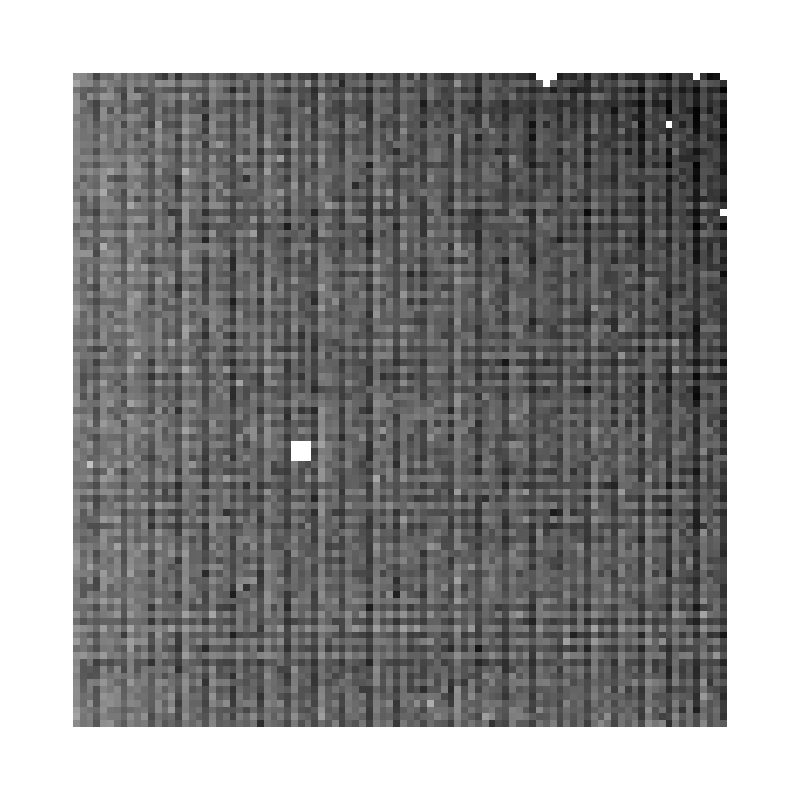

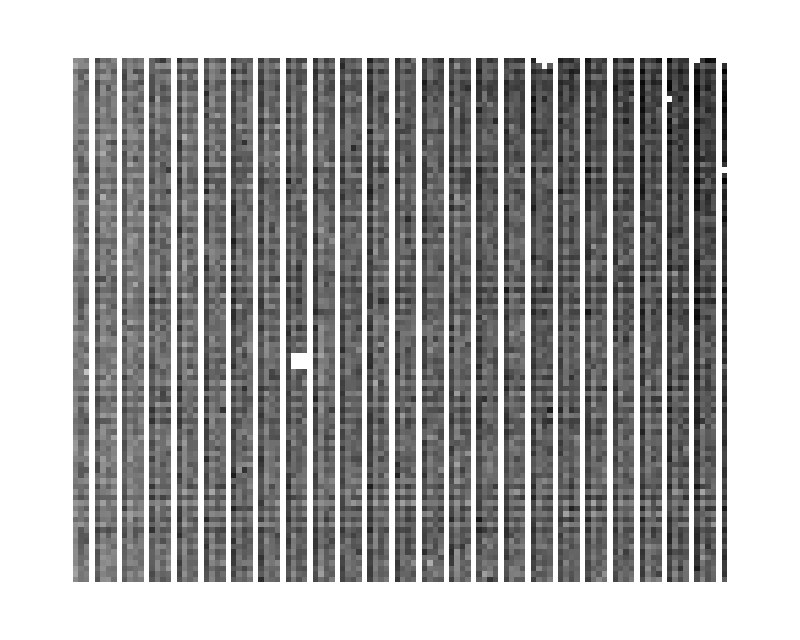

```mathematica
res1=resPre[[y;;yend,x;;xend]];
ArrayPlot[res1,PlotRange->{med-n,med+n},DataReversed->True,ImageSize->800]
res2=Last@postageDat;
ArrayPlot[res2,PlotRange->{med-n,med+n},DataReversed->True,ImageSize->800]
```

```mathematica
{cn,rn}
```

{423,259}

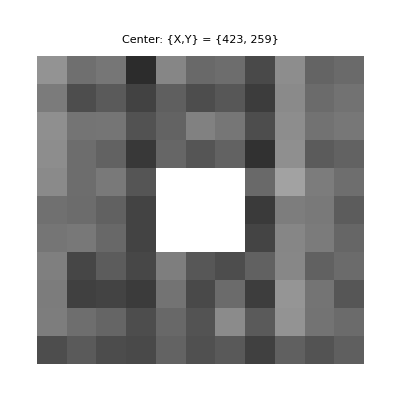

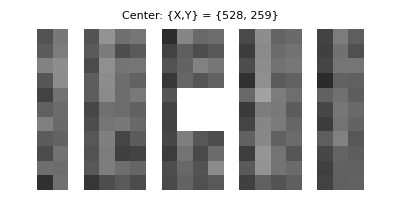

{Null}

-Graphics-

-Graphics-

{Null}

```mathematica
num=5;
Table[
{cn,rn}=partitionedPoses[[k]];
Print[ArrayPlot[resPre[[rn-num;;rn+num]][[;;,cn-num;;cn+num]],DataReversed->True,PlotRange->{med-n,med+n},PlotLabel->Style["Center: {X,Y} = "<>ToString@{cn,rn},18]]];
{cn2,rn2}=mapFun[{cn,rn}];
Print[ArrayPlot[Last[data][[rn2-num;;rn2+num]][[;;,cn2-2num;;cn2+2num]],DataReversed->True,PlotRange->{med-n,med+n},PlotLabel->Style["Center: {X,Y} = "<>ToString@{cn2,rn2},18]]];
,{k,Length@partitionedPoses}]
```

## Test Centroiding

### functions

#### other

```mathematica
Needs["Developer`"]
```

```mathematica
FFT[image_]:=FFTShift[Fourier[FFTShift[image]]];
IFFT[image_]:=FFTShift[InverseFourier[FFTShift[image]]];
FFTShift[image_]:=Module[{n,res},n=Dimensions[image][[1]];
res=RotateLeft[Transpose[RotateLeft[image,n/2]],n/2]]
Resize[PupReduite_List,n_]:=Module[{nReduit},nReduit=Dimensions[PupReduite][[1]];
If[nReduit<n,ToPackedArray[N[Agrandir[PupReduite,n]]],ToPackedArray[N[Reduction[PupReduite,n]]]]];
Agrandir[PupReduite_List,n_]:=Module[{Pupille,nReduit,n0},n0=n/2+1;
Pupille=Table[0.,{n},{n}];
nReduit=Dimensions[PupReduite][[1]];
Pupille[[Range[n0-nReduit/2,n0+nReduit/2-1],Range[n0-nReduit/2,n0+nReduit/2-1]]]=PupReduite;
Pupille];
Reduction[image_,nfinal_]:=Module[{n,n0},n=Dimensions[image][[1]];
n0=n/2+1;
image[[Range[n0-nfinal/2,n0+nfinal/2-1],Range[n0-nfinal/2,n0+nfinal/2-1]]]];
MakeDisk=Compile[{R1,n},Module[{i,j,n0},
n0=n/2+1;
N[Table[If[Sqrt[(i-n0)^2+(j-n0)^2]<R1,1,0],{i,n},{j,n}]]
]];
```

#### centroid

```mathematica
Options[Photocenter]={Verbose->True};
Photocenter[image_,ApproxCenter_,Radius_,OptionsPattern[]]:=Module[{mask,npix,pos,vals,lin,col},
npix=Length[image];
mask=Transpose[RotateLeft[Transpose[RotateLeft[MakeDisk[Radius,npix],(npix/2+1)-ApproxCenter[[2]]]],(npix/2+1)-ApproxCenter[[1]]]];
If[OptionValue[Verbose],Print[ArrayPlot[mask*image]]];
pos=Position[mask,_?(#==1&)];
vals=Extract[image,pos];
lin=N@(Total[pos[[All,1]]*vals]/Total[vals]);
col=N@(Total[pos[[All,2]]*vals]/Total[vals]);
{lin,col}
]
```

```mathematica
Options[FloatingWindowCentroid]={Verbose->True};
FloatingWindowCentroid[image_,ApproxCenter_,size_,OptionsPattern[]]:=Module[{xoff,yoff,mask,npix,pos,vals,x,y,window,n0,xcen,ycen,XWeights,YWeights,edgepixels,boxpixels,newweights,weights,weightsvals,iIndex,jIndex,xyHW},
xcen=ApproxCenter[[1]];
ycen=ApproxCenter[[2]];

npix=Length[image];
If[EvenQ[size],Print["error: size must be odd"];Abort[]];
XWeights=YWeights=Table[0,{size+2},{size+2}];
xyHW=(size-1)/2;
iIndex=Table[Table[k,{k,Round[xcen]-(xyHW+1),Round[xcen]+(xyHW+1)}],{kk,1,size+2}]//Transpose;
xoff=Abs[iIndex-xcen];
boxpixels=Position[xoff,_?(#<=xyHW&)];
edgepixels=Position[xoff,_?(xyHW<#<xyHW+1&)];
newweights=(xyHW+1-xoff);
Do[XWeights=ReplacePart[XWeights,edgepixels[[i]]->newweights[[edgepixels[[i,1]],edgepixels[[i,2]]]]],{i,Length[edgepixels]}];
Do[XWeights=ReplacePart[XWeights,boxpixels[[i]]->1],{i,Length[boxpixels]}];
(*Print[Reverse[XWeights]//TableForm];*)

jIndex=Table[Table[k,{k,Round[ycen]-(xyHW+1),Round[ycen]+(xyHW+1)}],{kk,1,size+2}];
yoff=Abs[jIndex-ycen];
boxpixels=Position[yoff,_?(#<=xyHW&)];
edgepixels=Position[yoff,_?(xyHW<#<xyHW+1&)];
newweights=(xyHW+1-yoff);
Do[YWeights=ReplacePart[YWeights,edgepixels[[i]]->newweights[[edgepixels[[i,1]],edgepixels[[i,2]]]]],{i,Length[edgepixels]}];
Do[YWeights=ReplacePart[YWeights,boxpixels[[i]]->1],{i,Length[boxpixels]}];
(*Print[Reverse[YWeights]//TableForm];*)

weights=Table[0,{npix},{npix}];
weights[[Range[Round[xcen]-(xyHW+1),Round[xcen]+(xyHW+1)],Range[Round[ycen]-(xyHW+1),Round[ycen]+(xyHW+1)]]]=XWeights*YWeights;(*Print[XWeights*YWeights//TableForm];*)
If[OptionValue[Verbose],Print[{ArrayPlot[Resize[Log[weights*image],32]],ArrayPlot[Resize[weights,32]]}]];
(*Print[Reverse[Resize[weights,16]]//TableForm];*)
pos=Position[weights,_?(#!=0&)];

vals=Extract[image,pos];
weightsvals=Extract[weights,pos];

x=N@(Total[pos[[All,1]]*vals*weightsvals]/Total[vals*weightsvals]);
y=N@(Total[pos[[All,2]]*vals*weightsvals]/Total[vals*weightsvals]);
{x,y}

];

Centroid[image_,{y0_,x0_},BoxSize_:7]:=Module[{CheckBox5image,x,y},
CheckBox5image=ImageFilter[Total[Flatten[#]]&,Image[image],2]//ImageData;
(*updated 3/28/2017 to have the reverse xy output to match directly DS9 and ArrayPlot coordinates*)
(*{x,y}=Position[CheckBox5image,Max[CheckBox5image]]//First;*)
{x,y}=FloatingWindowCentroid[image,{x0,y0},BoxSize,Verbose->False];
Do[
{x,y}=FloatingWindowCentroid[image,{x,y},BoxSize,Verbose->False],{k,1,15}];
{y,x}
]
```

```mathematica
(*updated 3/28/2017 to have the reverse xy output to match directly DS9 and ArrayPlot coordinates*)
CenterFun[image_,{xinit_,yinit_},boxsize_,tolerance_]:=Module[{posImage,dif,x,y,x0,y0},
posImage=image+Abs[Min@image];
dif=1;
{x,y}={xinit,yinit};
While[dif>tolerance,
{x0,y0}={x,y};
{x,y}=FloatingWindowCentroid[posImage,{x,y},boxsize,Verbose->False];
dif=Norm[{x,y}-{x0,y0}];];
{y,x}
]
```

```mathematica
ShiftImageInterp[image_,alpha_,beta_]:=Module[{tmp,n,res},n=Dimensions[image]//First;
tmp=ListInterpolation[image,InterpolationOrder->3,Method->"Spline"];
res=Table[tmp[y-alpha,x-beta],{y,1,n},{x,1,n}]]
```

```mathematica
(*updated 3/28/2017 to have the reverse xy output to match directly DS9 and ArrayPlot coordinates*)
AstroAndPhoto[finalImage_,{X_,Y_},PSF_,searchRadius_,{conjFFTPSF_,totPSF_,npix_},fftIm_,snrThresholdForFun_,ExpansionFactor_]:=Module[{h,f,res1,xPlanet1,yPlanet1,Position1,Signal1,FMCutOff,newX,newY},
FMCutOff=3ExpansionFactor;
h= (ExpansionFactor Re[IFFT[Resize[fftIm conjFFTPSF,npix ExpansionFactor]]] npix)/totPSF;
f=ListInterpolation[h,InterpolationOrder->3];
{newX,newY}=({X,Y}-(npix/2+1))*ExpansionFactor+((npix*ExpansionFactor)/2+1);
res1=FindMaximum[f[x,y],{x,newX,newX-FMCutOff,newX+FMCutOff},{y,newY,newY-FMCutOff,newY+FMCutOff},PrecisionGoal->3];{xPlanet1,yPlanet1}={res1[[2,1,2]],res1[[2,2,2]]};Position1={xPlanet1,yPlanet1};
If[Sqrt[Total[(Position1-{newX,newY})^2]]>ExpansionFactor*searchRadius,Position1={0.0,0.0};Signal1=0.0;,Position1=(Position1-((ExpansionFactor*npix)/2+1))/ExpansionFactor+(npix/2+1);Signal1=f[xPlanet1,yPlanet1];];
If[Signal1≤snrThresholdForFun,Signal1=0.0;];
{Reverse@Position1,Signal1}]
```

```mathematica
AstroAndPhotoPrep[psf_]:={Conjugate[FFT[psf]],Total[psf^2,2],Length@psf}
```

### astrophoto

```mathematica
Clear@smallcuts
```

```mathematica
smallcutSize=1;
p01=pointPose-smallcutSize-1;p02=pointPose+smallcutSize;
(*smallcuts=submat[#,p01,p02]&/@imdata;*)
sizeImage=2*smallcutSize+2
```

4

```mathematica
psf
```

{{16.697,330.698,609.311,330.698},{330.698,1687.01,2620.84,1687.01},{609.311,2620.84,3943.09,2620.84},{330.698,1687.01,2620.84,1687.01}}

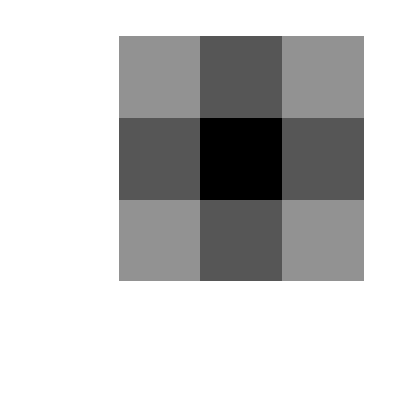

{4,4}

```mathematica
psf[[All,1]]={0,0,0,0};psf[[1]]={0,0,0,0};
psf=psf/Total[psf,2];
ArrayPlot[psf,DataReversed->True]
psf//Dimensions
```

```mathematica
snrThresholdForFun=0;ExpansionFactor=5;searchRadius=3;
{x0,y0}={(n+1)/2,(n+1)/2};
image=psf;
fftIm=FFT[image];
```

```mathematica
{x0,y0}={3,3}
AstroAndPhoto[image,{x0,y0},psf,searchRadius,AstroAndPhotoPrep[psf],fftIm,snrThresholdForFun,ExpansionFactor]
```

{3,3}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{3.,3.},1.}

```mathematica
searchRadius
```

3

```mathematica
Dimensions@image
```

{1280,1032}

```mathematica
psf=Resize[Abs[FFT[Resize[MakeDisk[100,200],500]]]^2,sizeImage];
```

```mathematica
dat=imdata00[[1;;numImsInGroup]];
image=dat[[1]];
fftIm=FFT[image];prep=AstroAndPhotoPrep[psf];
{x0,y0}={702,452};
AstroAndPhoto[image,{x0,y0},psf,searchRadius,prep,fftIm,snrThresholdForFun,ExpansionFactor]
```

Thread::tdlen: Objects of unequal length in {{200.829-397.368 ⅈ,-54.5121-552.545 ⅈ,-88.2905-261.641 ⅈ,-118.899-310.902 ⅈ,-186.28+312.036 ⅈ,362.144-264.47 ⅈ,698.454-56.6612 ⅈ,-256.235+252.631 ⅈ,-396.437-366.784 ⅈ,-212.637+50.8613 ⅈ,«32»,63.0147-542.481 ⅈ,266.099+99.5315 ⅈ,-407.162-40.4093 ⅈ,56.2641+79.5683 ⅈ,-661.971+230.113 ⅈ,-669.159-315.696 ⅈ,309.226+299.896 ⅈ,-109.826+234.696 ⅈ,«982»},{«1»},«48»,«1230»} {«1»} cannot be combined.

$Aborted

```mathematica
image==psf
```

True

```mathematica
Export["~/Desktop/testpsf.fits",psf]
```

~/Desktop/testpsf.fits

```mathematica
(*image*)
```

```mathematica
Off[General::stop];
```

```mathematica
mfVals=Table[
psfFromData=smallcuts[[alldaframes]][[k]];
psfFromData=psfFromData/Total[psfFromData,2];
(*ArrayPlot[psfFromData,DataReversed->True]*)
image=psfFromData;
fftIm=FFT[image];
rest=AstroAndPhoto[image,{x0,y0},psf,searchRadius,AstroAndPhotoPrep[psf],fftIm,snrThresholdForFun,ExpansionFactor][[1]];
rest,{k,Length@alldaframes}]
```

{{1.21765,1.06267},{1.31171,4.56011},{2.68879,3.38072},{3.01325,3.29919},{3.04869,3.27626},{3.06855,3.26233},{3.08133,3.25622},{3.08497,3.25404},{3.08425,3.25016},{3.0852,3.24693},{3.08655,3.24289},{3.08634,3.24202},{3.08527,3.24023},{3.08367,3.23886},{3.08308,3.23861},{3.08246,3.23682},{3.08192,3.23548},{3.08136,3.23423},{3.08201,3.23276},{3.08203,3.23135}}

3

3

```mathematica
mfRelVals=mfVals-(Length@psf/2+1)
```

{{-1.78498,-1.96547},{-1.70338,1.6239},{-0.268168,0.354054},{0.0216709,0.286846},{0.0541457,0.266984},{0.072734,0.25541},{0.0845014,0.2502},{0.0876712,0.248405},{0.0866777,0.244774},{0.0872353,0.24165},{0.0882316,0.237621},{0.0877326,0.236711},{0.0864438,0.234703},{0.0846098,0.233269},{0.0839433,0.232983},{0.0831328,0.231094},{0.0824056,0.22952},{0.0816186,0.228064},{0.0820512,0.226469},{0.0819044,0.223344}}

{701,451}

```mathematica
poseOfInterest=Last@partitionedPoses
```

{423,259}

{528,259}

```mathematica
finalres=mfRelVals+ConstantArray[mapFun[poseOfInterest],Length@mfRelVals]
finalresPre=mfRelVals+ConstantArray[poseOfInterest,Length@mfRelVals]
```

{{526.215,257.035},{526.297,260.624},{527.732,259.354},{528.022,259.287},{528.054,259.267},{528.073,259.255},{528.085,259.25},{528.088,259.248},{528.087,259.245},{528.087,259.242},{528.088,259.238},{528.088,259.237},{528.086,259.235},{528.085,259.233},{528.084,259.233},{528.083,259.231},{528.082,259.23},{528.082,259.228},{528.082,259.226},{528.082,259.223}}

{{421.215,257.035},{421.297,260.624},{422.732,259.354},{423.022,259.287},{423.054,259.267},{423.073,259.255},{423.085,259.25},{423.088,259.248},{423.087,259.245},{423.087,259.242},{423.088,259.238},{423.088,259.237},{423.086,259.235},{423.085,259.233},{423.084,259.233},{423.083,259.231},{423.082,259.23},{423.082,259.228},{423.082,259.226},{423.082,259.223}}

```mathematica
(mapFun/@finalresPre)==finalres
```

True

```mathematica
(*finalresPre-ConstantArray[{390,219},Length@finalresPre]*)
```

```mathematica
DirectoryName@nfn
```

/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/

```mathematica
tflist=#==poseOfInterest&/@Round[finalresPre]
```

{False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
datexp=Flatten/@Transpose@{Range@Length@finalresPre,finalresPre,tflist};
```

```mathematica
Export[DirectoryName@nfn<>"point_source_locations.csv",Prepend[datexp,{"Image Number","X (pix)","Y (pix)","Centroid Algorithm Success"}]]
```

/Users/hagan/Dropbox/STScI/Functional/MIRI/MIRI_Pipeline_Testing/MIRI_TA_code/OSS_Delivery/test/LRS/point_source_locations.csv

```mathematica
(*ListPlot[{relcentersFW,mfRelVals},AspectRatio->1,PlotRange->{{(*-0.5*)0,0.5},{(*-0.5*)0,0.5}}]*)
```

### coordinate check

```mathematica
smallcutSize=1;
p01=pointPose-smallcutSize-1;p02=pointPose+smallcutSize;
smallcuts=factor*submat[#,p01,p02]&/@imdata;
```

```mathematica
psfFromData=Last@smallcuts;
psfFromData=psfFromData/Total[psfFromData,2];
```

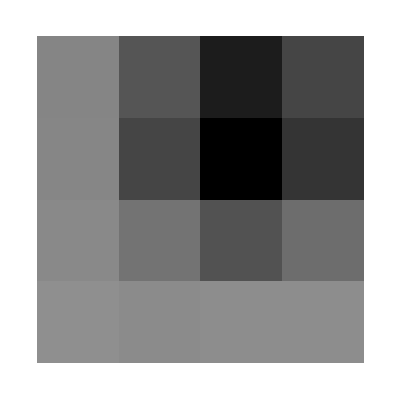

```mathematica
ArrayPlot[psfFromData,DataReversed->True]
```

```mathematica
snrThresholdForFun=0;ExpansionFactor=5;searchRadius=3;
{x0,y0}={15.0,16.0};
image=psf;
fftIm=FFT[image];
```

```mathematica
AstroAndPhoto[image,{x0,y0},psf,searchRadius,AstroAndPhotoPrep[psf],fftIm,snrThresholdForFun,ExpansionFactor]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{17.,17.},1.}

```mathematica
smallcutSize=1;
p01=pointPose-smallcutSize;p02=pointPose+smallcutSize;
smallcuts=factor*submat[#,p01,p02]&/@imdata;
sizeImage=2*smallcutSize+2;
```

```mathematica
Last@smallcuts//MatrixForm
```

(21142 | 26155 | 22028
28221 | 38608 | 30782
25694 | 34326 | 28220)

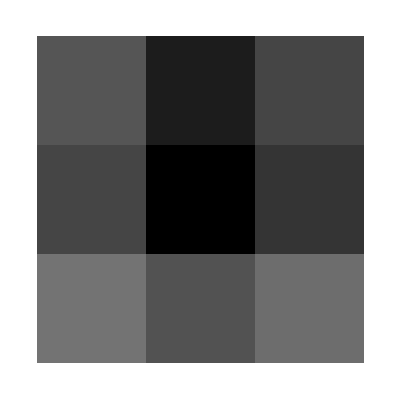

```mathematica
ArrayPlot[Last@smallcuts,DataReversed->True]
```

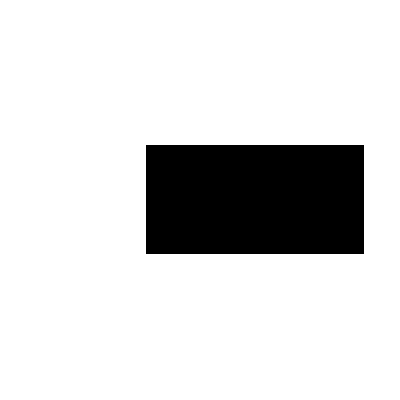

```mathematica
testmat=({{0, 0, 0}, {0, 1, 1}, {0, 0, 0}});
ArrayPlot[testmat,DataReversed->True]
```

```mathematica
n
```

3

```mathematica
xandys=Position[Partition[ConstantArray[1,n*n],n],1];
```

```mathematica
smvals=Flatten@testmat;
N[(#.smvals)/Total@smvals&/@Transpose@xandys]
```

{2.,2.5}

```mathematica
Export["~/Desktop/testmat.fits",testmat]
```

~/Desktop/testmat.fits

DS9 Center: {X,Y} = {2.5, 2}

```mathematica
({{21142, 26155, 22028}, {28221, 38608, 30782}, {25694, 34326, 28220}})
```

```mathematica
TRUEPOS={x+sum,}
```

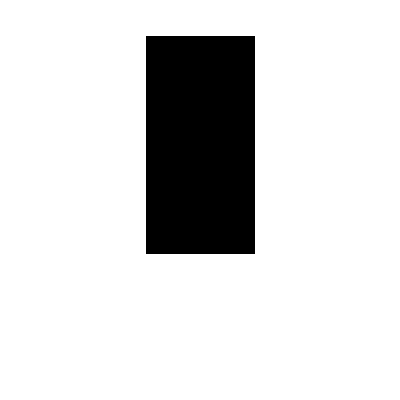

```mathematica
testmat=({{0, 0, 0}, {0, 1, 0}, {0, 1, 0}});
ArrayPlot[testmat,DataReversed->True]
```

```mathematica
xandys=Position[Partition[ConstantArray[1,n*n],n],1];
```

```mathematica
smvals=Flatten@testmat;
N[(#.smvals)/Total@smvals&/@Transpose@xandys]
```

{2.5,2.}

```mathematica
Export["~/Desktop/testmat.fits",testmat]
```

~/Desktop/testmat.fits

DS9 Center: {X,Y} = {2, 2.5}

Example:

```mathematica
({{21142, 26155, 22028}, {28221, 38608, 30782}, {25694, 34326, 28220}})
```

```mathematica
TRUEPOS={x+sum,y+sum}
```

Example above is HEAVIER in +Y than in +X